# Relative degree 2DOF

## Space robot

```mathematica
ClearAll["Global`*"]
```

```mathematica
x=({{q0[t]}, {q1[t]}, {q0'[t]}, {q1'[t]}});
```

#### Equation of motion Mx’’ + C = Hu

### Elements of Mass Matrix

```mathematica
m11=(4 I1 m0+4 I1 m1+4 l0^2 m0 m1+l1^2 m0 m1+4 I0 (m0+m1)+4 l0 l1 m0 m1 Cos[fi0-q1[t]])/(4 (m0+m1));
```

```mathematica
m12=(l1^2 m0 m1+4 I1 (m0+m1)+2 l0 l1 m0 m1 Cos[fi0-q1[t]])/(4 (m0+m1));
```

```mathematica
m21=(l1^2 m0 m1+4 I1 (m0+m1)+2 l0 l1 m0 m1 Cos[fi0-q1[t]])/(4 (m0+m1));
```

```mathematica
m22=(l1^2 m0 m1+4 I1 (m0+m1))/(4 (m0+m1));
```

### Elements of C Matrix

```mathematica
c1=(l0 l1 m0 m1 Sin[fi0-q1[t]] q1'[t] (2 q0'[t]+q1'[t]))/(2 (m0+m1));
```

```mathematica
c2=-(l0 l1 m0 m1 Sin[fi0-q1[t]] q0'[t]^2)/(2 (m0+m1));
```

```mathematica
M=({{m11, m12}, {m21, m22}});
```

```mathematica
B=({{c1}, {c2}});
```

```mathematica
H=({{0}, {1}});
u=u1;
```

#### x’ = f(x) + g(x)u

```mathematica
inv=Inverse[M].(H u-B);
```

```mathematica
xdot ={x[[3]], x[[4]],inv[[1]],inv[[2]]};
```

```mathematica
m0=40;m1=7;I0=6.667;I1=0.583;l0=1;l1=2;fi0=Pi/6;
```

## u1 input

```mathematica
gx=Coefficient[xdot,u1]//Simplify ;
```

```mathematica
fx=xdot-gx u1//Simplify//Chop;
```

### End effector x coordinate

```mathematica
hx=(2 l0 m0 Cos[fi0+q0[t]]+l1 (2 m0+m1) Cos[q0[t]+q1[t]])/(2 (m0+m1));
```

#### L_gh(x) k=0

```mathematica
Lghx=D[hx,Transpose[x]].gx
```

{0}

#### L_g L_fh(x) k=1

```mathematica
Lfhx=D[hx,Transpose[x]].fx
```

{1/94 (-80 Sin[π/6+q0[t]]-174 Sin[q0[t]+q1[t]]) q0'[t]-87/47 Sin[q0[t]+q1[t]] q1'[t]}

```mathematica
LgLfhx=D[Lfhx,Transpose[x]].gx//Simplify//Chop
```

{{(Sin[π/6+q0[t]] (-0.156837-0.123718 Cos[q1[t]]-0.0714286 Sin[q1[t]])+(0.658436+0.269086 Cos[q1[t]]+0.155357 Sin[q1[t]]) Sin[q0[t]+q1[t]])/(-2.32648+Cos[1/6 (π-6 q1[t])]^2)}}

```mathematica
SetOptions[ContourPlot,BaseStyle->{FontFamily->"LM Roman 10",FontSize->20,FontWeight->Bold}];
```

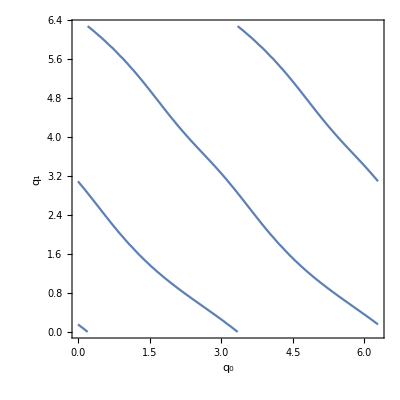

```mathematica
ContourPlot[LgLfhx==0,{q0[t],0,2 Pi},{q1[t],0,2 Pi},AxesLabel->{Subscript[q, 0],Subscript[q, 1]}]
```

```mathematica
subs=LgLfhx/.{q0[t]->0}//Simplify//Chop
s0=0;
```

{{(-0.0784186-0.061859 Cos[q1[t]]+0.622721 Sin[q1[t]]+0.155357 Sin[q1[t]]^2+0.134543 Sin[2 q1[t]])/(-2.32648+Cos[1/6 (π-6 q1[t])]^2)}}

```mathematica
sol=NSolve[subs==0,q1[t],Reals]/.C[1]->0
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{q1[t]→0.15355},{q1[t]→3.09553}}

```mathematica
val=q1[t]/.sol
```

{0.15355,3.09553}

```mathematica
s1=val[[1]];
```

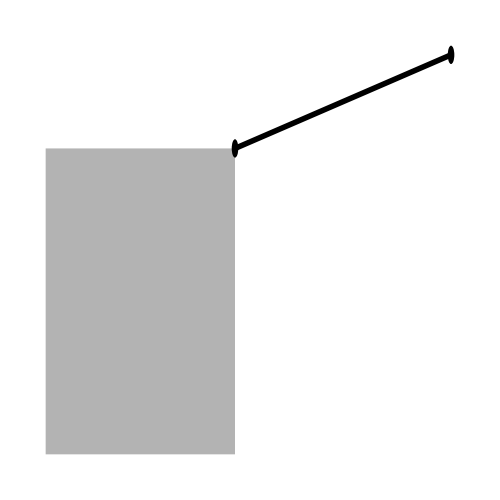

```mathematica
q0=s0; q1=s1;
Graphics[{GrayLevel[0.70],Thickness[0.008], Polygon[{{0,0},
                                                {+2l0 Cos[fi0] Cos[q0],2l0 Cos[fi0] Sin[q0]},
                                                {+2l0 Cos[q0+fi0],+2l0 Sin[q0+fi0]},
                                               {+2l0 Sin[fi0] Cos[q0+Pi/2],+2l0 Sin[fi0] Sin[q0+Pi/2]}}],
               Black,Thickness[0.008],Line[{{+2l0 Cos[q0+fi0],+2l0 Sin[q0+fi0]},
                                        {+2l0 Cos[q0+fi0]+l1 Cos[q0+q1],+2l0 Sin[q0+fi0]+l1 Sin[q0+q1]}}],
Black,Disk[{+2l0 Cos[q0+fi0],+2l0 Sin[q0+fi0]},0.03],
Black,Disk[{+2l0 Cos[q0+fi0]+l1 Cos[q0+q1],+2l0 Sin[q0+fi0]+l1 Sin[q0+q1]},0.03]},
ImageSize->{500,500}]
```

```mathematica
Clear[q0,q1];
```

#### ==> r>2 in these cases

#### L_g L_f^2h(x) k=2

```mathematica
Lf2hx=D[Lfhx,Transpose[x]].fx;
```

```mathematica
LgLf2hx=D[Lf2hx,Transpose[x]].gx;
```

```mathematica
subs=LgLf2hx/.{q0[t]->s0, q1[t]->s1, q0'[t]->0}//Simplify//Chop
s2=0;
```

{{{-1.25045 q1'[t]}}}

```mathematica
sol=Solve[subs==0,{q1'[t]}]
```

{{q1'[t]→0.}}

```mathematica
val2=q1'[t]/.sol
```

{0.}

```mathematica
s3=val2;
```

#### ==> r>3 in these cases

#### L_g L_f^3h(x) k=3

```mathematica
Lf3hx=D[Lf2hx,Transpose[x]].fx//Chop;
```

```mathematica
LgLf3hx=D[Lf3hx,Transpose[x]].gx//Chop;
```

```mathematica
subs=LgLf3hx/.{q0[t]->s0, q1[t]->s1,q0'[t]->s2,q1'[t]->s3}//Simplify//Chop
```

{{{{{0}}}}}

#### ==> r=4

### End effector y coordinate

```mathematica
hx=(2 l0 m0 Sin[fi0+q0[t]]+l1 (2 m0+m1) Sin[q0[t]+q1[t]])/(2 (m0+m1));
```

#### L_gh(x) k=0

```mathematica
Lghx=D[hx,Transpose[x]].gx
```

{0}

#### L_g L_fh(x) k=1

```mathematica
Lfhx=D[hx,Transpose[x]].fx
```

{1/94 (80 Cos[π/6+q0[t]]+174 Cos[q0[t]+q1[t]]) q0'[t]+87/47 Cos[q0[t]+q1[t]] q1'[t]}

```mathematica
LgLfhx=D[Lfhx,Transpose[x]].gx//Simplify//Chop
```

{{(Cos[q0[t]+q1[t]] (-0.658436-0.269086 Cos[q1[t]]-0.155357 Sin[q1[t]])+Cos[π/6+q0[t]] (0.156837+0.123718 Cos[q1[t]]+0.0714286 Sin[q1[t]]))/(-2.32648+Cos[1/6 (π-6 q1[t])]^2)}}

```mathematica
SetOptions[ContourPlot,BaseStyle->{FontFamily->"LM Roman 10",FontSize->20,FontWeight->Bold}];
```

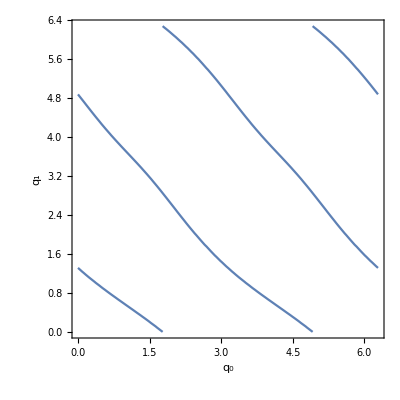

```mathematica
ContourPlot[LgLfhx==0,{q0[t],0,2 Pi},{q1[t],0,2 Pi},AxesLabel->{Subscript[q, 0],Subscript[q, 1]}]
```

```mathematica
subs=LgLfhx/.{q0[t]->0}//Simplify//Chop
s0=0;
```

{{(0.135825-0.551293 Cos[q1[t]]-0.269086 Cos[q1[t]]^2+0.061859 Sin[q1[t]]-0.0776786 Sin[2 q1[t]])/(-2.32648+Cos[1/6 (π-6 q1[t])]^2)}}

```mathematica
sol=NSolve[subs==0,q1[t],Reals]/.C[1]->0
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{q1[t]→-1.40123},{q1[t]→1.31386}}

```mathematica
val=q1[t]/.sol
```

{-1.40123,1.31386}

```mathematica
s1=val[[2]];
```

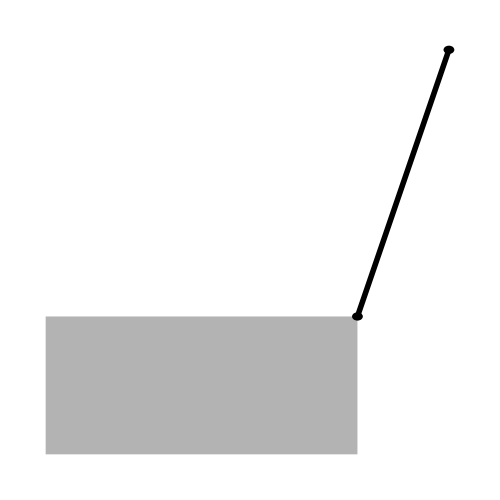

```mathematica
q0=s0; q1=s1;
Graphics[{GrayLevel[0.70],Thickness[0.008], Polygon[{{0,0},
                                                {+2l0 Cos[fi0] Cos[q0],2l0 Cos[fi0] Sin[q0]},
                                                {+2l0 Cos[q0+fi0],+2l0 Sin[q0+fi0]},
                                               {+2l0 Sin[fi0] Cos[q0+Pi/2],+2l0 Sin[fi0] Sin[q0+Pi/2]}}],
               Black,Thickness[0.008],Line[{{+2l0 Cos[q0+fi0],+2l0 Sin[q0+fi0]},
                                        {+2l0 Cos[q0+fi0]+l1 Cos[q0+q1],+2l0 Sin[q0+fi0]+l1 Sin[q0+q1]}}],
Black,Disk[{+2l0 Cos[q0+fi0],+2l0 Sin[q0+fi0]},0.03],
Black,Disk[{+2l0 Cos[q0+fi0]+l1 Cos[q0+q1],+2l0 Sin[q0+fi0]+l1 Sin[q0+q1]},0.03]},
ImageSize->{500,500}]
```

```mathematica
Clear[q0,q1];
```

#### ==> r>2 in these cases

#### L_g L_f^2h(x) k=2

```mathematica
Lf2hx=D[Lfhx,Transpose[x]].fx;
```

```mathematica
LgLf2hx=D[Lf2hx,Transpose[x]].gx;
```

```mathematica
subs=LgLf2hx/.{q0[t]->s0, q1[t]->s1, q0'[t]->0}//Simplify//Chop
s2=0;
```

{{{-0.830401 q1'[t]}}}

```mathematica
sol=Solve[subs==0,{q1'[t]}]
```

{{q1'[t]→0.}}

```mathematica
val2=q1'[t]/.sol
```

{0.}

```mathematica
s3=val2;
```

#### ==> r>3 in these cases

#### L_g L_f^3h(x) k=3

```mathematica
Lf3hx=D[Lf2hx,Transpose[x]].fx//Chop;
```

```mathematica
LgLf3hx=D[Lf3hx,Transpose[x]].gx//Chop;
```

```mathematica
subs=LgLf3hx/.{q0[t]->s0, q1[t]->s1,q0'[t]->s2,q1'[t]->s3}//Simplify//Chop
```

{{{{{0}}}}}

#### ==> r=4